```mathematica
sol3=DSolve[{D[u[x,t],{x,2}]==D[u[x,t],{t,2}],Derivative[0,1][u][x,0]==x Exp[-x^2],u[x,0]==0},u,{x,t}]
```

{{u→Function[{x,t},Piecewise[{{1/4 (ⅇ^(-(t-x)^2)-ⅇ^(-(t+x)^2)), t≥0}, {Indeterminate, True}}]]}}

```mathematica
sol4=DSolve[{D[u[x,t],{x,2}]==D[u[x,t],{t,2}],Derivative[0,1][u][x,0]==0,u[x,0]==x Exp[-x^2],u[0,t]==0},u,{x,t}]
```

{{u→Function[{x,t},Piecewise[{{1/2 (ⅇ^(-(-t+x)^2) (-t+x)+ⅇ^(-(t+x)^2) (t+x)), x>t≥0}, {1/2 (-ⅇ^(-(t-x)^2) (t-x)+ⅇ^(-(t+x)^2) (t+x)), 0≤x≤t}, {Indeterminate, True}}]]}}

```mathematica
(*Q3*)
```

```mathematica
Plot3D[u[x,t]/.sol3[[1]],{x,-3,3},{t,0,5},AxesLabel->Automatic]
```

-Graphics3D-

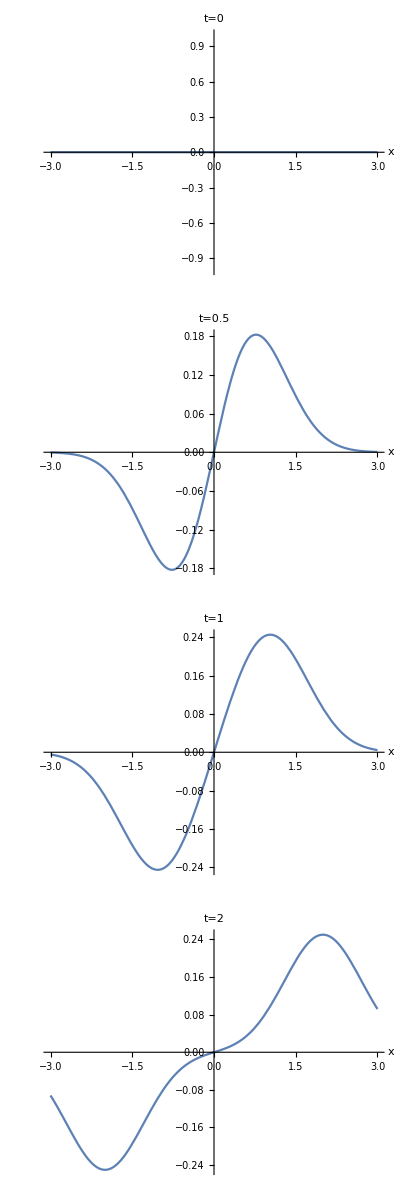

```mathematica
Plot[u[x,t]/.sol3[[1]]/.t->#,{x,-3,3},AxesLabel->Automatic,PlotLabel->"t="<>ToString@#,ImageSize->Medium]&/@{0,0.5,1,2}//TableForm
```

```mathematica
(*Q4*)
```

```mathematica
Plot3D[u[x,t]/.sol4[[1]],{x,0,5},{t,0,5},AxesLabel->Automatic]
```

-Graphics3D-

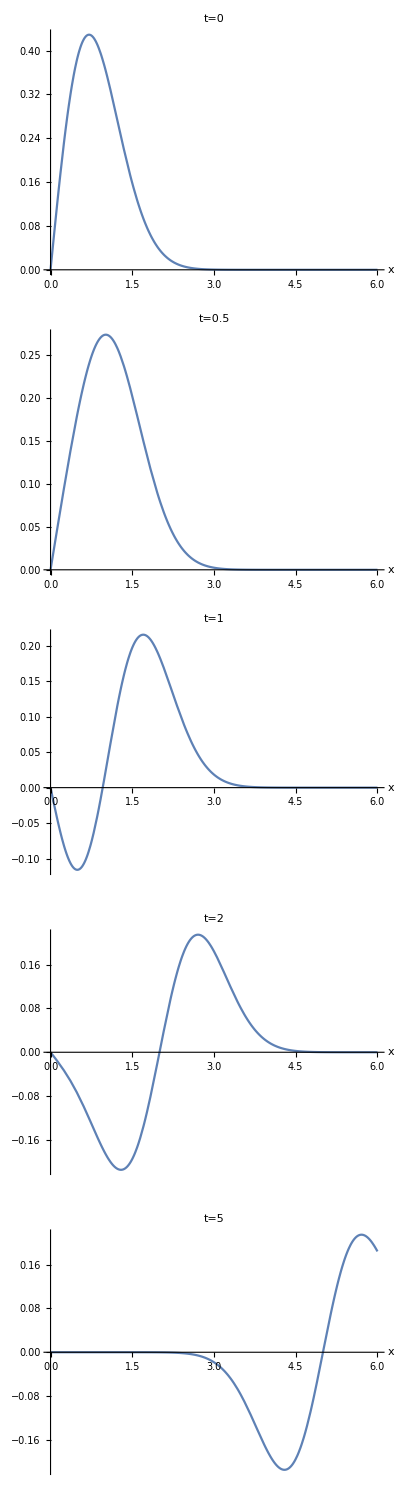

```mathematica
Plot[u[x,t]/.sol4[[1]]/.t->#,{x,0,6},AxesLabel->Automatic,PlotLabel->"t="<>ToString@#,ImageSize->Medium]&/@{0,0.5,1,2,5}//TableForm
```